Using E2 result as an approximation for the asymmetric rectification potential

Density on either side of cusp

```mathematica
p1=Exp[-1/2(a+1)^2 x^2-1/2 a(a+1)y^2+a(a+1)x y];
p2=Exp[-1/2 (L/l)^2(a (L/l)^2+1)^2 x^2-1/2 a(a (L/l)^2+1)y^2+a (L/l)^2(a (L/l)^2+1)x y];
```

```mathematica
norm=π/(√a)(1/(a+1)Erf[√((a+1)/2)L]+1/((L/l)(a(L/l)^2+1))Erf[√((a(L/l)^2+1)/2)L]);
(*I am interested near the cusp. The normalisation won't be quite right close to x=0, but hopefully this is just a shift rather than a distortion of the profile near the cusp*)
```

Full predicted eta distribution

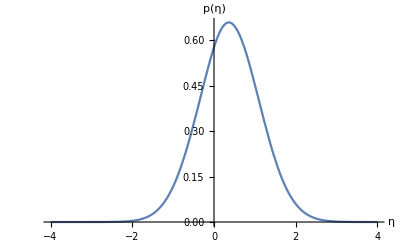

```mathematica
py=Integrate[p1,{x,0,L}]+Integrate[p2,{x,0,l}]//Simplify;
Plot[py/.{a->1,L->0.8,l->0.2},
{y,-4,4},
AxesLabel->{"η","p(η)"},
LabelStyle->Directive[FontSize->16]]
(*This asymmetry is not observed in simulation*)
```

Calculate currents at cusp

```mathematica
(*Jx=(η+f)ρ. Integrate this at the cusp to find total current which makes it over.*)
Jp=Assuming[a>0&&L>l>0,
Integrate[(y-L)*p1/.x->L,{y,L,∞}]]//Simplify
Jm=Assuming[a>0&&L>l>0,
Integrate[(y+L^2/l)*p2/.x->-l,{y,-L^2/l,-∞}]]//Simplify
Jp/=norm;
Jm/=norm;
```

(ⅇ^(-1/2 (1+a) L^2))/(a (1+a))

(ⅇ^(-1/2 L^2 (1+(a L^2)/l^2)) l^2)/(a (l^2+a L^2))

```mathematica
norm
```

(π (Erf[(√(1+a) L)/(√2)]/(1+a)+(l Erf[(L √(1+(a L^2)/l^2))/(√2)])/(L (1+(a L^2)/l^2))))/(√a)

Plot current left, current right, and total for given geometry

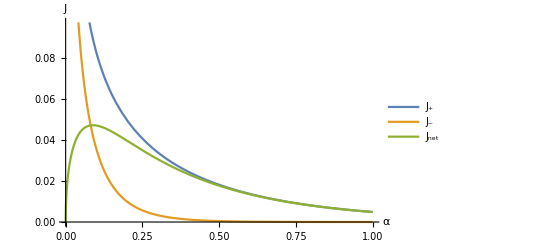

```mathematica
Plot[
{Jp,Jm,Jp-Jm}/.{L->2,l->1}//Evaluate,
{a,0,1},
PlotRange->{All,Automatic},
AxesLabel->{"α","J"},
LabelStyle->Directive[FontSize->16],
PlotLegends->{"J_+","J_-","J_net"}]
```

Plot total current for several geometries at fixed λ

```mathematica
pycolours={Blue,Green,Red,Cyan,Purple};
```

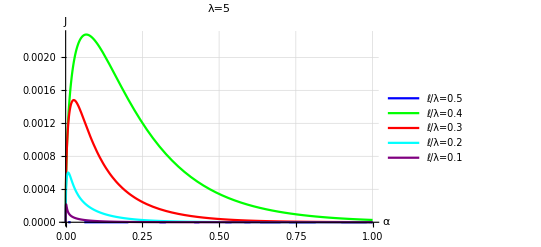

```mathematica
lam=5;
llist=Table[l,{l,0.1*lam,0.5*lam,0.1*lam}]//Reverse;
Jαplot=Plot[
Table[{Jp-Jm}/.{L->lam-llist[[i]],l->llist[[i]]},{i,1,Length[llist]}]//Evaluate,
{a,0,1},
PlotRange->{{0,0.5},{0,All}},
PlotLegends->Table["ℓ/λ="<>ToString[llist[[i]]/lam],{i,1,Length[llist]}],
PlotLabel->"λ="<>ToString[lam],
AxesLabel->{"α","J"},
TicksStyle->Directive[FontSize->14],LabelStyle->Directive[FontSize->16],
PlotStyle->pycolours,
PlotStyle->Thick,
GridLines->Automatic]
(*Export[NotebookDirectory[]<>"/Pressure/RECT/Theory/Ja_lam"<>ToString[lam]<>".pdf",%,ImageSize->{400,400}];*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.×10^-8,0.}.

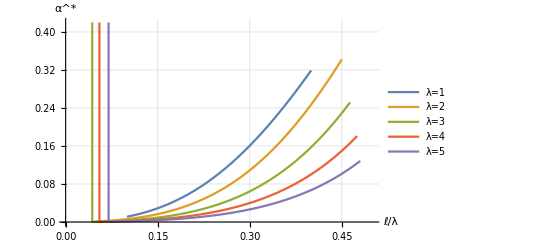

```mathematica
λlist={1,2,3,4,5};
llist=Range[Length[λlist]];
alist=Range[Length[λlist]];
For[j=1,j≤Length[λlist],j++,
λ=λlist[[j]];
llist[[j]]=Table[l,{l,0.1,0.5*λ-0.1,0.01*λ}];
alist[[j]]=Table[
a/.FindRoot[D[Jp-Jm,a]==0/.{L->λ-llist[[j,i]],l->llist[[j,i]]},{a,0.001},
MaxIterations->1000,AccuracyGoal->Infinity,PrecisionGoal->8],
{i,1,Length[llist[[j]]]}];
llist[[j]]/=λ;
]
alplot=ListPlot[
Table[Transpose[{llist[[j]],alist[[j]]}],{j,1,Length[λlist]}],
PlotRange->{{0,0.5},{0.0,Automatic}},
AxesLabel->{"ℓ/λ","α^*"},
PlotLegends->Table["λ="<>ToString[λlist[[j]]],{j,1,Length[λlist]}],
Joined->True,
LabelStyle->Directive[FontSize->16],
PlotStyle->Thick,
GridLines->Automatic]
Export[NotebookDirectory[]<>"/Pressure/RECT/Theory/allam.pdf",alplot];
```

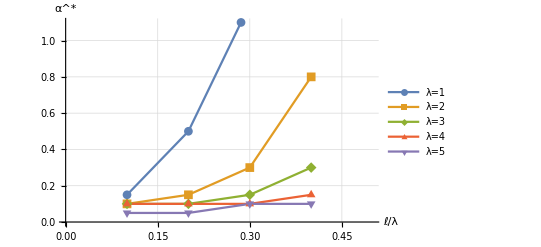

```mathematica
(*Data. λ=1,2,3,4,5. l/λ=0.1,0.2,0.3,0.4*)
λlist={1,2,3,4,5};
llist={0.1,0.2,0.3,0.4};
alist=
{{0.15,0.5,1.2,2.0},
{0.1,0.15,0.3,0.8},
{0.1,0.1,0.15,0.3},
{0.1,0.1,0.1,0.15},
{0.05,0.05,0.1,0.1}};
allamData=Table[{llist[[j]],alist[[i,j]]},{i,1,Length[λlist]},{j,1,Length[llist]}];
alSimPlot=ListPlot[
allamData,
Joined->True,PlotMarkers->{Automatic},
PlotRange->{{0,0.5},Automatic},
AxesLabel->{"ℓ/λ","α^*"},
PlotLegends->{"λ=1","λ=2","λ=3","λ=4","λ=5"},
LabelStyle->Directive[FontSize->16],
PlotStyle->Thick,
GridLines->Automatic]
Export[NotebookDirectory[]<>"/Pressure/RECT/Theory/allamSim.pdf",alSimPlot];
```

```mathematica
Graphics[{Text@Style[Subscript[ℓ,""],30,#]},ImageSize->50]&/@{"TR","SR","MR","MB"}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ell=(Graphics[{Text@Style[Subscript[ℓ,""],30,#]},ImageSize->50]&/@{"MR"})[[1]]
ToString[ell]
```

-Graphics-

-Graphics-